Matern générale

```mathematica
signP[x_]=Piecewise[{{-1,x<0}},1]
```

Piecewise[{{-1, x<0}, {1, True}}]

```mathematica
ff[x_,v_]:=x^v*BesselK[v,x]
gg[x_,v_,l_]:=Sqrt[2*v]*Abs[x]/l
AA[v_]:=2^(1-v)/Gamma[v]
```

```mathematica
dff[x_,v_]:=-x^v*BesselK[v-1,x]
ddff[x_,v_]:=-x^(v-1)*BesselK[v-1,x]+x^v*BesselK[v-2,x]
```

```mathematica
dgg[x_,v_,l_]:=Sqrt[2*v]*signP[x]/l
ddgg[x_,v_,l_]:=0
```

```mathematica
m[x_,v_,l_]:=AA[v]*ff[gg[x,v,l],v]
dm[x_,v_,l_]:=AA[v]*dgg[x,v,l]*dff[gg[x,v,l],v]
ddm[x_,v_,l_]:=AA[v]*(ddgg[x,v,l]*dff[gg[x,v,l],v]+dgg[x,v,l]^2*ddff[gg[x,v,l],v])
```

```mathematica
dgg[0,vv,ll]
```

(√2 √vv)/ll

```mathematica
hh[x_]=m[x,vv,ll]
```

(2^(1-vv/2) ((√vv)/ll)^vv Abs[x]^vv BesselK[vv,(√2 √vv Abs[x])/ll])/Gamma[vv]

```mathematica
(2+1/Abs[x])*Abs[x]//Simplify
```

1+2 Abs[x]

```mathematica
(2+1/Abs[x])*Abs[x]
```

(2+1/Abs[x]) Abs[x]

```mathematica
Simplify[ddm[x,v,l],x≥0]
```

(2^(3/2-v/2) ((√v)/l)^(1+v) x^(-1+v) (√2 √v x BesselK[-2+v,(√2 √v x)/l]-l BesselK[-1+v,(√2 √v x)/l]))/(l Gamma[v])

```mathematica
ddm[x,5/2,l]//FullSimplify
aggg[x]
```

-(5 ⅇ^(-(√5 Abs[x])/l) (l^2+√5 l Abs[x]-5 x Conjugate[x]))/(3 l^4)

aggg[x]

```mathematica
vv=1.1;ll=0.4;
p[x_]=m[x,vv,ll]//Simplify;
dp[x_]=dm[x,vv,ll]//Simplify;
ddp[x_]=Simplify[ddm[x,vv,ll]];
Plot[p[x],{x,-2,2},PlotRange->All]
Plot[dp[x],{x,-2,2},PlotRange->All]
Plot[ddp[x],{x,-2,2},PlotRange->All]

ddp[0]
```

```mathematica
Limit[x^v*BesselK[v-1,x]/.v->2,x->0]
```

0

```mathematica
ff[x,v]
dff[x,v]
ddff[x,v]
```

x^v BesselK[v,x]

-x^v BesselK[-1+v,x]

x^v BesselK[-2+v,x]-x^(-1+v) BesselK[-1+v,x]

```mathematica
d
```

```mathematica
Animate[Plot[m[x,vu,lv],{x,-2,2},PlotRange->All],{vu,0.1,2},{lv,0.1,5},AnimationRunning->False]
```

```mathematica
Animate[Plot[dm[x,vu,lv],{x,-2,2},PlotRange->All],{vu,0.1,5},{lv,0.1,5},AnimationRunning->False]
```

```mathematica
Animate[Plot[ddm[x,vu,lv],{x,-2,2},PlotRange->All],{vu,3/2,5},{lv,0.1,5},AnimationRunning->False]
```

```mathematica
,
```

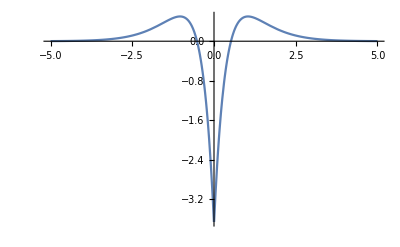

```mathematica
Plot[ddm[x,3/2,0.9],{x,-5,5},PlotRange->All]
```

```mathematica
hh[x_]:=2^(1-n)/Gamma[n]*(Sqrt[2*n]*x/ll)^n*BesselK[n,x]
```

```mathematica
D[hh[x],x]//Simplify
hh''[x]//Simplify
```

-(1.76777^n (√n x)^n (x BesselK[-1+n,x]-2 n BesselK[n,x]+x BesselK[1+n,x]))/(x Gamma[n])

1/(2 x^2 Gamma[n])1.76777^n (√n x)^n (x^2 BesselK[-2+n,x]-4 n x BesselK[-1+n,x]-4 n BesselK[n,x]+4 n^2 BesselK[n,x]+2 x^2 BesselK[n,x]-4 n x BesselK[1+n,x]+x^2 BesselK[2+n,x])

```mathematica
n=1;ll=1;
```

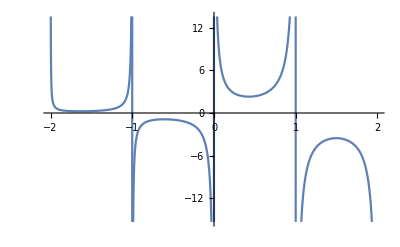

```mathematica
Plot[Gamma[x-2],{x,-2,2}]
```

```mathematica
Gamma[0]
```

ComplexInfinity